```mathematica
ϵ=0
```

0

```mathematica
g1 = x^2 + (5(y-3)/4 -Sqrt[x^2+ϵ])^2
```

x^2+(-√(x^2)+5/4 (-3+y))^2

```mathematica
g2 = (2(a-3)^2+2(b-4)^2)^3-40(a-3)^2(b-4)^2
```

(2 (-3+a)^2+2 (-4+b)^2)^3-40 (-3+a)^2 (-4+b)^2

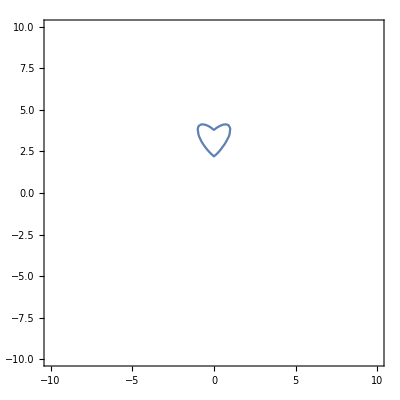

```mathematica
ahoj1 = ContourPlot[g1==1,{x,-10,10},{y,-10,10}]
```

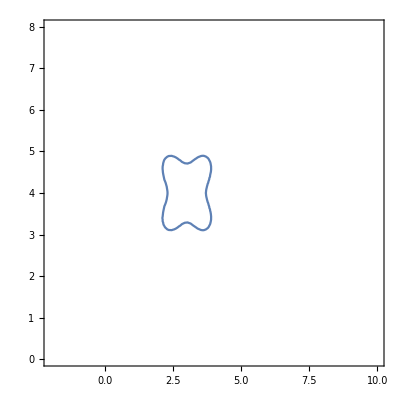

```mathematica
ahoj2 = ContourPlot[g2==1,{a,-2,10},{b,0,8}]
```

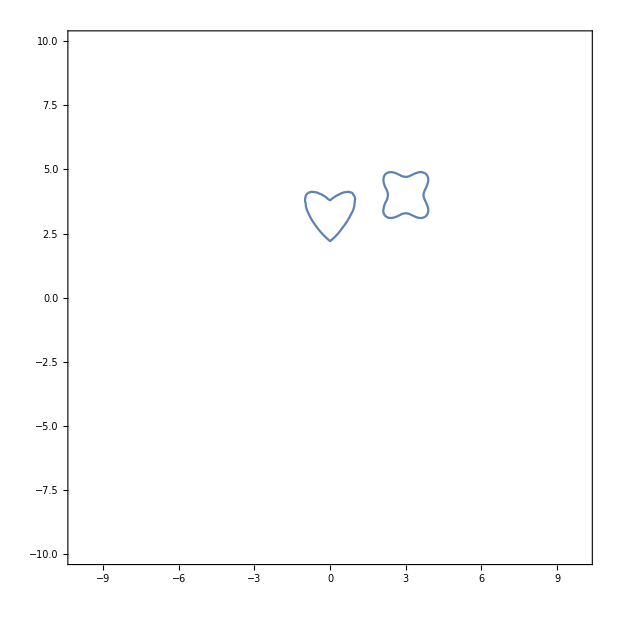

```mathematica
Show[ahoj1,ahoj2]
```

```mathematica
min = (x-a)^2+(y-b)^2
```

(-a+x)^2+(-b+y)^2

```mathematica
pokus =FindMinimum[{min,g1≤1,g2≤1},{x,y,a,b}]
```

{1.29599,{x→0.988257,y→3.66837,a→2.11105,b→3.48042}}

```mathematica
bod1 =Point[{x,y}/.Last[pokus]]
```

Point[{0.988257,3.66837}]

```mathematica
bod2 = Point[{a,b}/.Last[pokus]]
```

Point[{2.11105,3.48042}]

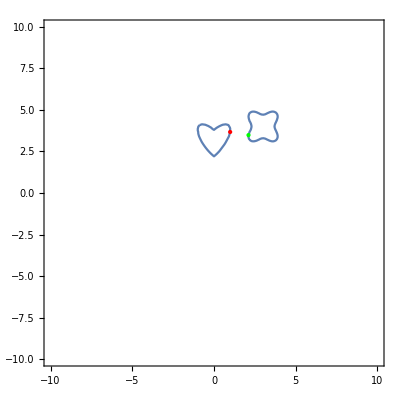

```mathematica
Show[ahoj1,ahoj2,Graphics[{Red,PointSize[Large],bod1}],Graphics[{Green, PointSize[Large],bod2}]]
```